## Simplified FK of SRSPM

```mathematica
SetDirectory[NotebookDirectory[]]
(*<<ed5314utils_en.m*)
```

/home/adityak/Aditya/git/root_tracking/Mathematica/SRSPM/FK

```mathematica
rotZ[θ_]:={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
```

```mathematica
(*fixed platform*)
b1 = {1, 0, 0};
b2 = rotZ[2*0.2985].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
tempa = Table[Symbol["b"<>ToString[i]],{i, 6}];
b = Table[tempa[[i]],{i, Length[tempa]}];
bshift=b-{b[[1]],b[[1]],b[[1]],b[[1]],b[[1]],b[[1]]}//N
```

{{0.,0.,0.},{-0.172974,0.562164,0.},{-1.5,0.866025,0.},{-1.90036,0.435143,0.},{-1.5,-0.866025,0.},{-0.926665,-0.997307,0.}}

```mathematica
(*moving platform*)
a1 = {0.5803, 0, 0};
a2 = rotZ[2*0.6573].a1;
a3 = rotZ[2π/3].a1;
a4 = rotZ[2π/3].a2;
a5 = rotZ[4π/3].a1;
a6 = rotZ[4π/3].a2;
tempa = Table[Symbol["a"<>ToString[i]],{i, 6}];
a = Table[tempa[[i]],{i, Length[tempa]}];
ashift=a-{a[[1]],a[[1]],a[[1]],a[[1]],a[[1]],a[[1]]}//N
```

{{0.,0.,0.},{-0.43325,0.561359,0.},{-0.87045,0.502555,0.},{-1.13998,-0.153331,0.},{-0.87045,-0.502555,0.},{-0.167673,-0.408029,0.}}

```mathematica
lvals ={1.298717863895003,1.5716396210384063,1.5812238031942756,1.4545807927904213,1.2290739802091717,1.3918829703985098}
```

{1.29872,1.57164,1.58122,1.45458,1.22907,1.39188}

```mathematica
l = {l1, l2, l3, l4, l5, l6}
```

{l1,l2,l3,l4,l5,l6}

```mathematica
sub=Join[Inner[Rule,{b1x,b1y,b1z,b2x,b2y,b2z,b3x,b3y,b3z,b4x,b4y,b4z,b5x,b5y,b5z,b6x,b6y,b6z},Flatten[bshift],List],Inner[Rule,{t1x,t1y,t1z,t2x,t2y,t2z,t3x,t3y,t3z,t4x,t4y,t4z,t5x,t5y,t5z,t6x,t6y,t6z},Flatten[ashift],List]]
len=Inner[Rule, l, lvals, List]
```

{b1x→0.,b1y→0.,b1z→0.,b2x→-0.172974,b2y→0.562164,b2z→0.,b3x→-1.5,b3y→0.866025,b3z→0.,b4x→-1.90036,b4y→0.435143,b4z→0.,b5x→-1.5,b5y→-0.866025,b5z→0.,b6x→-0.926665,b6y→-0.997307,b6z→0.,t1x→0.,t1y→0.,t1z→0.,t2x→-0.43325,t2y→0.561359,t2z→0.,t3x→-0.87045,t3y→0.502555,t3z→0.,t4x→-1.13998,t4y→-0.153331,t4z→0.,t5x→-0.87045,t5y→-0.502555,t5z→0.,t6x→-0.167673,t6y→-0.408029,t6z→0.}

{l1→1.29872,l2→1.57164,l3→1.58122,l4→1.45458,l5→1.22907,l6→1.39188}

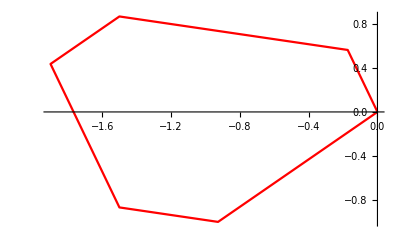

```mathematica
(*Fixed Platform*)
o1={0,0,0};
o2={b2x,b2y,b2z};
o3={b3x,b3y,b3z};
o4={b4x,b4y,b4z};
o5={b5x,b5y,b5z};
o6={b6x,b6y,b6z};
o={o1,o2,o3,o4,o5,o6,o1};
ListLinePlot[(o/.sub)[[;;, 1;;2]],PlotStyle->Red]
(*oj={bjx,bjy,bjz};*)
```

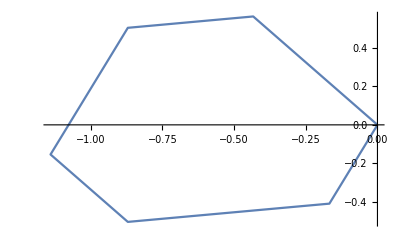

```mathematica
(*Moving platform*)
p1={0,0,0};
p2={t2x,t2y,t2z};
p3={t3x,t3y,t3z};
p4={t4x,t4y,t4z};
p5={t5x,t5y,t5z};
p6={t6x,t6y,t6z};
p={p1,p2,p3,p4,p5,p6,p1};
ListLinePlot[(p/.sub)[[;;, 1;;2]]]
(*pj={tjx,tjy,tjz};*)
```

```mathematica
Cmat={{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}}
```

{{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}}

```mathematica
Rmat=Simplify[(IdentityMatrix[3]+Cmat).Inverse[(IdentityMatrix[3]-Cmat)]];
```

```mathematica
xvec={x,y,z};
```

```mathematica
p1o=xvec+Rmat.p1;
p2o=xvec+Rmat.p2;
p3o=xvec+Rmat.p3;
p4o=xvec+Rmat.p4;
p5o=xvec+Rmat.p5;
p6o=xvec+Rmat.p6;
(*pjo=xvec+Rmat.pj;*)
```

```mathematica
eq1=(p1o-o1).(p1o-o1)-l1^2
```

-l1^2+x^2+y^2+z^2

```mathematica
(*monoprod[{a_,b_}]:=a.b;
eqj=FullSimplify[monoprod[FullSimplify[monopoly[Factor[(pjo-oj).(pjo-oj)-lj^2][[3]],{bjx,bjy,bjz,tjx,tjy,tjz,lj}]]/.{ (x^2+y^2+z^2)-> w,1+c1^2+c2^2+c3^2-> c0,-1-c1^2-c2^2-c3^2-> -c0}]];*)
```

```mathematica
eq2=FullSimplify[Factor[(p2o-o2).(p2o-o2)-l2^2][[3]]];
eq3=FullSimplify[Factor[(p3o-o3).(p3o-o3)-l3^2][[3]]];
eq4=FullSimplify[Factor[(p4o-o4).(p4o-o4)-l4^2][[3]]];
eq5=FullSimplify[Factor[(p5o-o5).(p5o-o5)-l5^2][[3]]];
eq6=FullSimplify[Factor[(p6o-o6).(p6o-o6)-l6^2][[3]]];
```

```mathematica
nsol=Timing[NSolve[N[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len),50]=={0,0,0,0,0,0},{x,y,z,c1,c2,c3},Method-> "HomotopyContinuation"]];
```

$Aborted

```mathematica
len
```

{l1→1.29872,l2→1.57164,l3→1.58122,l4→1.45458,l5→1.22907,l6→1.39188}

```mathematica
Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.#)] ]&/@nsol[[2]](*Residue check*)
```

{1.14181×10^20,1.14181×10^20,7.40635×10^19,7.40635×10^19,3.60977×10^20,3.60977×10^20,1.08295×10^20,1.08295×10^20,1.14181×10^20,1.14181×10^20,7.40635×10^19,7.40635×10^19,3.60977×10^20,3.60977×10^20,1.08295×10^20,1.08295×10^20,1.47038×10^18,1.47038×10^18,2.70781×10^17,2.70781×10^17,1.19152×10^18,1.19152×10^18,2.26779×10^18,2.26779×10^18,9.04762×10^17,9.04762×10^17,2.01798×10^19,2.01798×10^19,8.03609×10^19,8.03609×10^19,3.73039×10^17,3.73039×10^17,1.09397×10^18,1.09397×10^18,1.02686×10^18,1.02686×10^18,9.51353×10^17,9.51353×10^17,6.76953×10^17,6.76953×10^17,9.04762×10^17,9.04762×10^17,2.01798×10^19,2.01798×10^19,8.03609×10^19,8.03609×10^19,3.73039×10^17,3.73039×10^17,8.34402×10^16,8.34402×10^16,3.11619×10^16,3.11619×10^16,3.93995×10^16,3.93995×10^16,1.09065×10^17,1.09065×10^17,5.4508×10^16,5.4508×10^16,5.04373×10^16,5.04373×10^16,4.02726×10^16,4.02726×10^16,5.80955×10^16,5.80955×10^16,3.61221×10^16,3.61221×10^16,1.57393×10^16,1.57393×10^16,1.36365×10^16,1.36365×10^16,4.12816×10^16,4.12816×10^16,1.57393×10^16,1.57393×10^16,4.12816×10^16,4.12816×10^16,3.61221×10^16,3.61221×10^16,1.36365×10^16,1.36365×10^16,4.02726×10^16,4.02726×10^16,5.4508×10^16,5.4508×10^16,5.80955×10^16,5.80955×10^16,5.04373×10^16,5.04373×10^16,4.65409×10^16,4.65409×10^16,3.54137×10^14,3.54137×10^14,9.05004×10^14,9.05004×10^14,3.10371×10^18,3.10371×10^18,4.18593×10^17,4.18593×10^17,4.48905×10^17,4.48905×10^17,4.48905×10^17,4.48905×10^17,5.30751×10^15,5.30751×10^15,5.30751×10^15,5.30751×10^15,1.24834×10^16,1.24834×10^16,1.75332×10^16,1.75332×10^16,1.75332×10^16,1.75332×10^16,3.60375×10^15,3.60375×10^15,312985.,312985.,997950.,997950.,997950.,997950.,211285.,211285.,219466.,219466.,219466.,219466.,69956.1,69956.1,69956.1,69956.1,66557.1,66557.1,1.1545×10^-13,1.1545×10^-13,1.34259×10^-14,1.34259×10^-14,1.01268×10^-14,1.01268×10^-14,6.93462×10^-14,6.93462×10^-14,3.51259×10^-15,3.51259×10^-15,1.12434×10^-14,1.12434×10^-14,5.0865×10^-14,5.0865×10^-14,4.14814×10^-15,5.0865×10^-14,5.0865×10^-14,1.75717×10^-15,1.75717×10^-15,3.9674×10^-15,2.37732×10^-15,2.37732×10^-15,6.58691×10^-15,1.13764×10^-15,1.13764×10^-15,3.9674×10^-15,6.58691×10^-15,4.14814×10^-15}

```mathematica
nsol[[2]][[3]]
```

{x→-2.28056×10^17-7.28995×10^17 ⅈ,y→7.26736×10^17-2.2371×10^17 ⅈ,z→-6.62991×10^16+5.54034×10^16 ⅈ,c1→0.772379-0.517395 ⅈ,c2→0.554854+0.875733 ⅈ,c3→-0.0920629+0.937177 ⅈ}

```mathematica
Select[c3/.nsol[[2]],Abs[Im[#]]≤ 10^-6&](*Reals filter*)
```

{-1.21096+3.63837×10^-46 ⅈ,-1.21096-3.63837×10^-46 ⅈ,0.825788+3.22506×10^-45 ⅈ,0.825788-3.22506×10^-45 ⅈ,0.825788+3.22506×10^-45 ⅈ,0.825788-3.22506×10^-45 ⅈ,-1.21096+3.63837×10^-46 ⅈ,-1.21096-3.63837×10^-46 ⅈ,1.67247+2.03915×10^-44 ⅈ,1.67247-2.03915×10^-44 ⅈ,-0.597917-1.59238×10^-45 ⅈ,-0.597917+1.59238×10^-45 ⅈ,-0.597917-1.59238×10^-45 ⅈ,-0.597917+1.59238×10^-45 ⅈ,1.67247+2.03915×10^-44 ⅈ,1.67247-2.03915×10^-44 ⅈ,-3.22454-1.58744×10^-43 ⅈ,-3.22454+1.58744×10^-43 ⅈ,0.310122+5.0145×10^-45 ⅈ,0.310122-5.0145×10^-45 ⅈ,0.310122+5.01449×10^-45 ⅈ,0.310122-5.01449×10^-45 ⅈ,-3.22454-1.58744×10^-43 ⅈ,-3.22454+1.58744×10^-43 ⅈ,48.9051-6.80081×10^-41 ⅈ,48.9051+6.80081×10^-41 ⅈ,-0.0204478,-0.0204478,-0.0204478,-0.0204478,48.9051-6.80081×10^-41 ⅈ,48.9051+6.80081×10^-41 ⅈ,286092.-3.96041×10^-30 ⅈ,286092.+3.96041×10^-30 ⅈ,-221217.+2.30705×10^-30 ⅈ,-221217.-2.30705×10^-30 ⅈ,194308.+9.19437×10^-29 ⅈ,194308.-9.19437×10^-29 ⅈ,-1.35802×10^-6-6.12215×10^-49 ⅈ,-1.35802×10^-6+6.12215×10^-49 ⅈ,1.7563×10^-6-8.9461×10^-47 ⅈ,1.7563×10^-6+8.9461×10^-47 ⅈ,-1.99952×10^-6+3.89787×10^-47 ⅈ,-1.99952×10^-6-3.89787×10^-47 ⅈ,8.41381+1.01307×10^-29 ⅈ,8.41381-1.01307×10^-29 ⅈ,-0.282677-3.95772×10^-32 ⅈ,-0.282677+3.95772×10^-32 ⅈ,-0.307926-2.86708×10^-31 ⅈ,-0.307926+2.86708×10^-31 ⅈ,7.28204+4.33862×10^-29 ⅈ,7.28204-4.33862×10^-29 ⅈ,0.0803994-5.08157×10^-32 ⅈ,0.0803994+5.08157×10^-32 ⅈ,-0.583355-4.80155×10^-31 ⅈ,-0.583355+4.80155×10^-31 ⅈ,0.278264,0.0862037-1.18858×10^-31 ⅈ,0.0862037+1.18858×10^-31 ⅈ,0.284389,0.18135,0.18135,0.495752,0.0648631+5.4488×10^-32 ⅈ,0.0648631-5.4488×10^-32 ⅈ,0.284389,0.495752,0.278264}

```mathematica
(*Coefficient[Times@@(α{2,4,4,4,4,4}),α^6]
Coefficient[Times@@(α{2,3,3,3,3,3}),α^6]
Coefficient[Times@@(α{2,2,2,2,2,2}+β{0,2,2,2,2,2}),α^3 β^3]
Coefficient[Times@@(α{2,1,1,1,1,1}+β{0,2,2,2,2,2}),α^3 β^3]*)(*multi-homogenoeus Bezout number calculation for different grouping and formulation*)
```

## Use these solutions till I figure out how to get the others

```mathematica
reqsol=nsol[[2,-28;;]];
```

```mathematica
(* Residue check *)
Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.#)] ]&/@reqsol
```

{1.1545×10^-13,1.1545×10^-13,1.34259×10^-14,1.34259×10^-14,1.01268×10^-14,1.01268×10^-14,6.93462×10^-14,6.93462×10^-14,3.51259×10^-15,3.51259×10^-15,1.12434×10^-14,1.12434×10^-14,5.0865×10^-14,5.0865×10^-14,4.14814×10^-15,5.0865×10^-14,5.0865×10^-14,1.75717×10^-15,1.75717×10^-15,3.9674×10^-15,2.37732×10^-15,2.37732×10^-15,6.58691×10^-15,1.13764×10^-15,1.13764×10^-15,3.9674×10^-15,6.58691×10^-15,4.14814×10^-15}

### These are solutions for the center of the moving platform

```mathematica
transformedsol=Table[Inner[Rule,{x,y,z,c1,c2,c3},(Join[({1,0,0}+{x,y,z}-Rmat.{0.5803,0,0}),{c1,c2,c3}]/.reqsol[[ii]]),List],{ii,1,28}];
```

```mathematica
(* x y z c1 c2 c3 *)
```

```mathematica
transformedsol//MatrixForm
```

(x→0.698494-1.34969×10^-29 ⅈ | y→-1.5474+3.4853×10^-30 ⅈ | z→-1.1973×10^-29-1.39961 ⅈ | c1→-2.43733×10^-30+2.71423 ⅈ | c2→8.07304×10^-30-3.8193 ⅈ | c3→8.41381+1.01307×10^-29 ⅈ
x→0.698494+1.34969×10^-29 ⅈ | y→-1.5474-3.4853×10^-30 ⅈ | z→-1.1973×10^-29+1.39961 ⅈ | c1→-2.43733×10^-30-2.71423 ⅈ | c2→8.07304×10^-30+3.8193 ⅈ | c3→8.41381-1.01307×10^-29 ⅈ
x→-1.49563+3.72461×10^-30 ⅈ | y→-2.08804-1.75142×10^-30 ⅈ | z→1.44469×10^-30-2.36321 ⅈ | c1→-6.28566×10^-31-0.55168 ⅈ | c2→-3.3889×10^-31-1.56523 ⅈ | c3→-0.282677-3.95772×10^-32 ⅈ
x→-1.49563-3.72461×10^-30 ⅈ | y→-2.08804+1.75142×10^-30 ⅈ | z→1.44469×10^-30+2.36321 ⅈ | c1→-6.28566×10^-31+0.55168 ⅈ | c2→-3.3889×10^-31+1.56523 ⅈ | c3→-0.282677+3.95772×10^-32 ⅈ
x→2.7712-2.01044×10^-30 ⅈ | y→-2.19661+1.22772×10^-30 ⅈ | z→-3.0454×10^-30-3.05059 ⅈ | c1→-1.23046×10^-30+1.65762 ⅈ | c2→7.47244×10^-31+0.413603 ⅈ | c3→-0.307926-2.86708×10^-31 ⅈ
x→2.7712+2.01044×10^-30 ⅈ | y→-2.19661-1.22772×10^-30 ⅈ | z→-3.0454×10^-30+3.05059 ⅈ | c1→-1.23046×10^-30-1.65762 ⅈ | c2→7.47244×10^-31-0.413603 ⅈ | c3→-0.307926+2.86708×10^-31 ⅈ
x→0.0629928-2.84661×10^-29 ⅈ | y→-0.965022+8.57832×10^-31 ⅈ | z→-2.74614×10^-29+0.72462 ⅈ | c1→-2.0297×10^-29+3.151 ⅈ | c2→1.162×10^-29-0.982358 ⅈ | c3→7.28204+4.33862×10^-29 ⅈ
x→0.0629928+2.84661×10^-29 ⅈ | y→-0.965022-8.57832×10^-31 ⅈ | z→-2.74614×10^-29-0.72462 ⅈ | c1→-2.0297×10^-29-3.151 ⅈ | c2→1.162×10^-29+0.982358 ⅈ | c3→7.28204-4.33862×10^-29 ⅈ
x→1.92327+6.83091×10^-30 ⅈ | y→-1.12966+3.3026×10^-30 ⅈ | z→5.09064×10^-30-0.701189 ⅈ | c1→-1.6393×10^-31-0.172892 ⅈ | c2→1.20333×10^-30+0.707344 ⅈ | c3→0.0803994-5.08157×10^-32 ⅈ
x→1.92327-6.83091×10^-30 ⅈ | y→-1.12966-3.3026×10^-30 ⅈ | z→5.09064×10^-30+0.701189 ⅈ | c1→-1.6393×10^-31+0.172892 ⅈ | c2→1.20333×10^-30-0.707344 ⅈ | c3→0.0803994+5.08157×10^-32 ⅈ
x→-0.509637+5.50591×10^-31 ⅈ | y→1.81322-7.1961×10^-31 ⅈ | z→2.43573×10^-31+2.07679 ⅈ | c1→-1.26164×10^-30+1.3507 ⅈ | c2→9.60039×10^-31-1.72376 ⅈ | c3→-0.583355-4.80155×10^-31 ⅈ
x→-0.509637-5.50591×10^-31 ⅈ | y→1.81322+7.1961×10^-31 ⅈ | z→2.43573×10^-31-2.07679 ⅈ | c1→-1.26164×10^-30-1.3507 ⅈ | c2→9.60039×10^-31+1.72376 ⅈ | c3→-0.583355+4.80155×10^-31 ⅈ
x→0.32474-0.062057 ⅈ | y→-0.998458-0.0837397 ⅈ | z→0.0441015-0.284416 ⅈ | c1→1.49985+0.0515166 ⅈ | c2→1.88359+0.331741 ⅈ | c3→4.47862-0.462864 ⅈ
x→0.32474+0.062057 ⅈ | y→-0.998458+0.0837397 ⅈ | z→0.0441015+0.284416 ⅈ | c1→1.49985-0.0515166 ⅈ | c2→1.88359-0.331741 ⅈ | c3→4.47862+0.462864 ⅈ
x→-0.264218 | y→-0.328347 | z→-1.13799 | c1→-0.0170775 | c2→-0.755342 | c3→0.278264
x→0.32474-0.062057 ⅈ | y→-0.998458-0.0837397 ⅈ | z→-0.0441015+0.284416 ⅈ | c1→-1.49985-0.0515166 ⅈ | c2→-1.88359-0.331741 ⅈ | c3→4.47862-0.462864 ⅈ
x→0.32474+0.062057 ⅈ | y→-0.998458+0.0837397 ⅈ | z→-0.0441015-0.284416 ⅈ | c1→-1.49985+0.0515166 ⅈ | c2→-1.88359+0.331741 ⅈ | c3→4.47862+0.462864 ⅈ
x→-0.486494+7.28143×10^-31 ⅈ | y→1.55542+1.20995×10^-30 ⅈ | z→-7.50437×10^-31-1.11929 ⅈ | c1→-2.60979×10^-31-0.574203 ⅈ | c2→-1.97216×10^-31-0.408785 ⅈ | c3→0.0862037-1.18858×10^-31 ⅈ
x→-0.486494-7.28143×10^-31 ⅈ | y→1.55542-1.20995×10^-30 ⅈ | z→-7.50437×10^-31+1.11929 ⅈ | c1→-2.60979×10^-31+0.574203 ⅈ | c2→-1.97216×10^-31+0.408785 ⅈ | c3→0.0862037+1.18858×10^-31 ⅈ
x→0.86686 | y→-0.474422 | z→1.06175 | c1→0.776908 | c2→0.00905767 | c3→0.284389
x→0.307256 | y→-0.365749 | z→1.36483 | c1→0.171204 | c2→0.109567 | c3→0.18135
x→0.307256 | y→-0.365749 | z→-1.36483 | c1→-0.171204 | c2→-0.109567 | c3→0.18135
x→0.218346 | y→-1.3675 | z→0.442814 | c1→-0.81007 | c2→-1.01713 | c3→0.495752
x→-0.836667-3.2315×10^-31 ⅈ | y→-2.08659-1.93407×10^-30 ⅈ | z→1.96891×10^-30-0.894832 ⅈ | c1→-4.44428×10^-31+0.685776 ⅈ | c2→5.12922×10^-32-0.386923 ⅈ | c3→0.0648631+5.4488×10^-32 ⅈ
x→-0.836667+3.2315×10^-31 ⅈ | y→-2.08659+1.93407×10^-30 ⅈ | z→1.96891×10^-30+0.894832 ⅈ | c1→-4.44428×10^-31-0.685776 ⅈ | c2→5.12922×10^-32+0.386923 ⅈ | c3→0.0648631-5.4488×10^-32 ⅈ
x→0.86686 | y→-0.474422 | z→-1.06175 | c1→-0.776908 | c2→-0.00905767 | c3→0.284389
x→0.218346 | y→-1.3675 | z→-0.442814 | c1→0.81007 | c2→1.01713 | c3→0.495752
x→-0.264218 | y→-0.328347 | z→1.13799 | c1→0.0170775 | c2→0.755342 | c3→0.278264)

```mathematica
Chop[transformedsol]//MatrixForm
```

(x→0.698494 | y→-1.5474 | z→0.-1.39961 ⅈ | c1→0.+2.71423 ⅈ | c2→0.-3.8193 ⅈ | c3→8.41381
x→0.698494 | y→-1.5474 | z→0.+1.39961 ⅈ | c1→0.-2.71423 ⅈ | c2→0.+3.8193 ⅈ | c3→8.41381
x→-1.49563 | y→-2.08804 | z→0.-2.36321 ⅈ | c1→0.-0.55168 ⅈ | c2→0.-1.56523 ⅈ | c3→-0.282677
x→-1.49563 | y→-2.08804 | z→0.+2.36321 ⅈ | c1→0.+0.55168 ⅈ | c2→0.+1.56523 ⅈ | c3→-0.282677
x→2.7712 | y→-2.19661 | z→0.-3.05059 ⅈ | c1→0.+1.65762 ⅈ | c2→0.+0.413603 ⅈ | c3→-0.307926
x→2.7712 | y→-2.19661 | z→0.+3.05059 ⅈ | c1→0.-1.65762 ⅈ | c2→0.-0.413603 ⅈ | c3→-0.307926
x→0.0629928 | y→-0.965022 | z→0.+0.72462 ⅈ | c1→0.+3.151 ⅈ | c2→0.-0.982358 ⅈ | c3→7.28204
x→0.0629928 | y→-0.965022 | z→0.-0.72462 ⅈ | c1→0.-3.151 ⅈ | c2→0.+0.982358 ⅈ | c3→7.28204
x→1.92327 | y→-1.12966 | z→0.-0.701189 ⅈ | c1→0.-0.172892 ⅈ | c2→0.+0.707344 ⅈ | c3→0.0803994
x→1.92327 | y→-1.12966 | z→0.+0.701189 ⅈ | c1→0.+0.172892 ⅈ | c2→0.-0.707344 ⅈ | c3→0.0803994
x→-0.509637 | y→1.81322 | z→0.+2.07679 ⅈ | c1→0.+1.3507 ⅈ | c2→0.-1.72376 ⅈ | c3→-0.583355
x→-0.509637 | y→1.81322 | z→0.-2.07679 ⅈ | c1→0.-1.3507 ⅈ | c2→0.+1.72376 ⅈ | c3→-0.583355
x→0.32474-0.062057 ⅈ | y→-0.998458-0.0837397 ⅈ | z→0.0441015-0.284416 ⅈ | c1→1.49985+0.0515166 ⅈ | c2→1.88359+0.331741 ⅈ | c3→4.47862-0.462864 ⅈ
x→0.32474+0.062057 ⅈ | y→-0.998458+0.0837397 ⅈ | z→0.0441015+0.284416 ⅈ | c1→1.49985-0.0515166 ⅈ | c2→1.88359-0.331741 ⅈ | c3→4.47862+0.462864 ⅈ
x→-0.264218 | y→-0.328347 | z→-1.13799 | c1→-0.0170775 | c2→-0.755342 | c3→0.278264
x→0.32474-0.062057 ⅈ | y→-0.998458-0.0837397 ⅈ | z→-0.0441015+0.284416 ⅈ | c1→-1.49985-0.0515166 ⅈ | c2→-1.88359-0.331741 ⅈ | c3→4.47862-0.462864 ⅈ
x→0.32474+0.062057 ⅈ | y→-0.998458+0.0837397 ⅈ | z→-0.0441015-0.284416 ⅈ | c1→-1.49985+0.0515166 ⅈ | c2→-1.88359+0.331741 ⅈ | c3→4.47862+0.462864 ⅈ
x→-0.486494 | y→1.55542 | z→0.-1.11929 ⅈ | c1→0.-0.574203 ⅈ | c2→0.-0.408785 ⅈ | c3→0.0862037
x→-0.486494 | y→1.55542 | z→0.+1.11929 ⅈ | c1→0.+0.574203 ⅈ | c2→0.+0.408785 ⅈ | c3→0.0862037
x→0.86686 | y→-0.474422 | z→1.06175 | c1→0.776908 | c2→0.00905767 | c3→0.284389
x→0.307256 | y→-0.365749 | z→1.36483 | c1→0.171204 | c2→0.109567 | c3→0.18135
x→0.307256 | y→-0.365749 | z→-1.36483 | c1→-0.171204 | c2→-0.109567 | c3→0.18135
x→0.218346 | y→-1.3675 | z→0.442814 | c1→-0.81007 | c2→-1.01713 | c3→0.495752
x→-0.836667 | y→-2.08659 | z→0.-0.894832 ⅈ | c1→0.+0.685776 ⅈ | c2→0.-0.386923 ⅈ | c3→0.0648631
x→-0.836667 | y→-2.08659 | z→0.+0.894832 ⅈ | c1→0.-0.685776 ⅈ | c2→0.+0.386923 ⅈ | c3→0.0648631
x→0.86686 | y→-0.474422 | z→-1.06175 | c1→-0.776908 | c2→-0.00905767 | c3→0.284389
x→0.218346 | y→-1.3675 | z→-0.442814 | c1→0.81007 | c2→1.01713 | c3→0.495752
x→-0.264218 | y→-0.328347 | z→1.13799 | c1→0.0170775 | c2→0.755342 | c3→0.278264)

```mathematica
roots = transformedsol
```

{{x→0.698494-1.34969×10^-29 ⅈ,y→-1.5474+3.4853×10^-30 ⅈ,z→-1.1973×10^-29-1.39961 ⅈ,c1→-2.43733×10^-30+2.71423 ⅈ,c2→8.07304×10^-30-3.8193 ⅈ,c3→8.41381+1.01307×10^-29 ⅈ},{x→0.698494+1.34969×10^-29 ⅈ,y→-1.5474-3.4853×10^-30 ⅈ,z→-1.1973×10^-29+1.39961 ⅈ,c1→-2.43733×10^-30-2.71423 ⅈ,c2→8.07304×10^-30+3.8193 ⅈ,c3→8.41381-1.01307×10^-29 ⅈ},{x→-1.49563+3.72461×10^-30 ⅈ,y→-2.08804-1.75142×10^-30 ⅈ,z→1.44469×10^-30-2.36321 ⅈ,c1→-6.28566×10^-31-0.55168 ⅈ,c2→-3.3889×10^-31-1.56523 ⅈ,c3→-0.282677-3.95772×10^-32 ⅈ},{x→-1.49563-3.72461×10^-30 ⅈ,y→-2.08804+1.75142×10^-30 ⅈ,z→1.44469×10^-30+2.36321 ⅈ,c1→-6.28566×10^-31+0.55168 ⅈ,c2→-3.3889×10^-31+1.56523 ⅈ,c3→-0.282677+3.95772×10^-32 ⅈ},{x→2.7712-2.01044×10^-30 ⅈ,y→-2.19661+1.22772×10^-30 ⅈ,z→-3.0454×10^-30-3.05059 ⅈ,c1→-1.23046×10^-30+1.65762 ⅈ,c2→7.47244×10^-31+0.413603 ⅈ,c3→-0.307926-2.86708×10^-31 ⅈ},{x→2.7712+2.01044×10^-30 ⅈ,y→-2.19661-1.22772×10^-30 ⅈ,z→-3.0454×10^-30+3.05059 ⅈ,c1→-1.23046×10^-30-1.65762 ⅈ,c2→7.47244×10^-31-0.413603 ⅈ,c3→-0.307926+2.86708×10^-31 ⅈ},{x→0.0629928-2.84661×10^-29 ⅈ,y→-0.965022+8.57832×10^-31 ⅈ,z→-2.74614×10^-29+0.72462 ⅈ,c1→-2.0297×10^-29+3.151 ⅈ,c2→1.162×10^-29-0.982358 ⅈ,c3→7.28204+4.33862×10^-29 ⅈ},{x→0.0629928+2.84661×10^-29 ⅈ,y→-0.965022-8.57832×10^-31 ⅈ,z→-2.74614×10^-29-0.72462 ⅈ,c1→-2.0297×10^-29-3.151 ⅈ,c2→1.162×10^-29+0.982358 ⅈ,c3→7.28204-4.33862×10^-29 ⅈ},{x→1.92327+6.83091×10^-30 ⅈ,y→-1.12966+3.3026×10^-30 ⅈ,z→5.09064×10^-30-0.701189 ⅈ,c1→-1.6393×10^-31-0.172892 ⅈ,c2→1.20333×10^-30+0.707344 ⅈ,c3→0.0803994-5.08157×10^-32 ⅈ},{x→1.92327-6.83091×10^-30 ⅈ,y→-1.12966-3.3026×10^-30 ⅈ,z→5.09064×10^-30+0.701189 ⅈ,c1→-1.6393×10^-31+0.172892 ⅈ,c2→1.20333×10^-30-0.707344 ⅈ,c3→0.0803994+5.08157×10^-32 ⅈ},{x→-0.509637+5.50591×10^-31 ⅈ,y→1.81322-7.1961×10^-31 ⅈ,z→2.43573×10^-31+2.07679 ⅈ,c1→-1.26164×10^-30+1.3507 ⅈ,c2→9.60039×10^-31-1.72376 ⅈ,c3→-0.583355-4.80155×10^-31 ⅈ},{x→-0.509637-5.50591×10^-31 ⅈ,y→1.81322+7.1961×10^-31 ⅈ,z→2.43573×10^-31-2.07679 ⅈ,c1→-1.26164×10^-30-1.3507 ⅈ,c2→9.60039×10^-31+1.72376 ⅈ,c3→-0.583355+4.80155×10^-31 ⅈ},{x→0.32474-0.062057 ⅈ,y→-0.998458-0.0837397 ⅈ,z→0.0441015-0.284416 ⅈ,c1→1.49985+0.0515166 ⅈ,c2→1.88359+0.331741 ⅈ,c3→4.47862-0.462864 ⅈ},{x→0.32474+0.062057 ⅈ,y→-0.998458+0.0837397 ⅈ,z→0.0441015+0.284416 ⅈ,c1→1.49985-0.0515166 ⅈ,c2→1.88359-0.331741 ⅈ,c3→4.47862+0.462864 ⅈ},{x→-0.264218,y→-0.328347,z→-1.13799,c1→-0.0170775,c2→-0.755342,c3→0.278264},{x→0.32474-0.062057 ⅈ,y→-0.998458-0.0837397 ⅈ,z→-0.0441015+0.284416 ⅈ,c1→-1.49985-0.0515166 ⅈ,c2→-1.88359-0.331741 ⅈ,c3→4.47862-0.462864 ⅈ},{x→0.32474+0.062057 ⅈ,y→-0.998458+0.0837397 ⅈ,z→-0.0441015-0.284416 ⅈ,c1→-1.49985+0.0515166 ⅈ,c2→-1.88359+0.331741 ⅈ,c3→4.47862+0.462864 ⅈ},{x→-0.486494+7.28143×10^-31 ⅈ,y→1.55542+1.20995×10^-30 ⅈ,z→-7.50437×10^-31-1.11929 ⅈ,c1→-2.60979×10^-31-0.574203 ⅈ,c2→-1.97216×10^-31-0.408785 ⅈ,c3→0.0862037-1.18858×10^-31 ⅈ},{x→-0.486494-7.28143×10^-31 ⅈ,y→1.55542-1.20995×10^-30 ⅈ,z→-7.50437×10^-31+1.11929 ⅈ,c1→-2.60979×10^-31+0.574203 ⅈ,c2→-1.97216×10^-31+0.408785 ⅈ,c3→0.0862037+1.18858×10^-31 ⅈ},{x→0.86686,y→-0.474422,z→1.06175,c1→0.776908,c2→0.00905767,c3→0.284389},{x→0.307256,y→-0.365749,z→1.36483,c1→0.171204,c2→0.109567,c3→0.18135},{x→0.307256,y→-0.365749,z→-1.36483,c1→-0.171204,c2→-0.109567,c3→0.18135},{x→0.218346,y→-1.3675,z→0.442814,c1→-0.81007,c2→-1.01713,c3→0.495752},{x→-0.836667-3.2315×10^-31 ⅈ,y→-2.08659-1.93407×10^-30 ⅈ,z→1.96891×10^-30-0.894832 ⅈ,c1→-4.44428×10^-31+0.685776 ⅈ,c2→5.12922×10^-32-0.386923 ⅈ,c3→0.0648631+5.4488×10^-32 ⅈ},{x→-0.836667+3.2315×10^-31 ⅈ,y→-2.08659+1.93407×10^-30 ⅈ,z→1.96891×10^-30+0.894832 ⅈ,c1→-4.44428×10^-31-0.685776 ⅈ,c2→5.12922×10^-32+0.386923 ⅈ,c3→0.0648631-5.4488×10^-32 ⅈ},{x→0.86686,y→-0.474422,z→-1.06175,c1→-0.776908,c2→-0.00905767,c3→0.284389},{x→0.218346,y→-1.3675,z→-0.442814,c1→0.81007,c2→1.01713,c3→0.495752},{x→-0.264218,y→-0.328347,z→1.13799,c1→0.0170775,c2→0.755342,c3→0.278264}}

```mathematica
Join[{roots[[15]]},roots[[20;;23]], roots[[26;;]]]//Chop
```

{{x→-0.264218,y→-0.328347,z→-1.13799,c1→-0.0170775,c2→-0.755342,c3→0.278264},{x→0.86686,y→-0.474422,z→1.06175,c1→0.776908,c2→0.00905767,c3→0.284389},{x→0.307256,y→-0.365749,z→1.36483,c1→0.171204,c2→0.109567,c3→0.18135},{x→0.307256,y→-0.365749,z→-1.36483,c1→-0.171204,c2→-0.109567,c3→0.18135},{x→0.218346,y→-1.3675,z→0.442814,c1→-0.81007,c2→-1.01713,c3→0.495752},{x→0.86686,y→-0.474422,z→-1.06175,c1→-0.776908,c2→-0.00905767,c3→0.284389},{x→0.218346,y→-1.3675,z→-0.442814,c1→0.81007,c2→1.01713,c3→0.495752},{x→-0.264218,y→-0.328347,z→1.13799,c1→0.0170775,c2→0.755342,c3→0.278264}}